# HW zero Name: Dhruvit Manojkumar Mavani

## 3) Import matrix

```mathematica
A = Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/gemat/gemat12.mtx.gz"]
```

SparseArray[…]

1)  Plotting of matrix A and computing % of non-zeroes

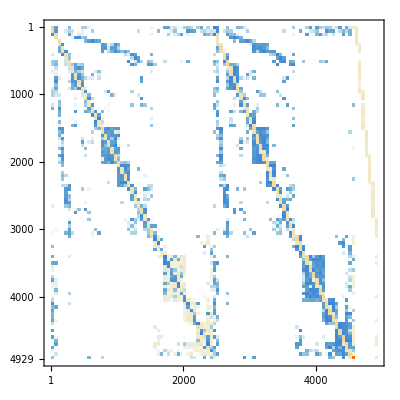

```mathematica
MatrixPlot[A]
```

```mathematica
33044./4929^2
```

0.00136011

2) Defining b

```mathematica
b = Normal[SparseArray[1->1,4929]];
```

3) Compute third largest magnitude Eigenvalue of A

```mathematica
Eigenvalues[A,{3}]
```

{5.2894-1.20544 ⅈ}

4) Solve Ax = b

```mathematica
x = Inverse[A].Transpose[b];
x[[3]]
```

1.11486